```mathematica
B ={{1-(a^2/(sigmaX*sigmaY)),(-a*b)/(sigmaX*sigmaY)},{(-a*b)/(sigmaX*sigmaY),1-(b^2/(sigmaX*sigmaY))}}
```

{{1-a^2/(sigmaX sigmaY),-(a b)/(sigmaX sigmaY)},{-(a b)/(sigmaX sigmaY),1-b^2/(sigmaX sigmaY)}}

```mathematica
{vals,vecs}=Eigensystem[B]
```

{{1,(-a^2-b^2+sigmaX sigmaY)/(sigmaX sigmaY)},{{-b/a,1},{a/b,1}}}

```mathematica
betacrit[a_,b_,sigmaX_,sigmaY_]:=1/(1-vals[[2]])
```

```mathematica
func[a_,b_,sigmaX_,sigmaY_]=Simplify[betacrit[a,b,sigmaX,sigmaY]]
```

(sigmaX sigmaY)/(a^2+b^2)

```mathematica
Plot3D[func[a,b,1,1],{a,-1,1},{b,-1,1},AxesLabel->{a,b}]
```

-Graphics3D-

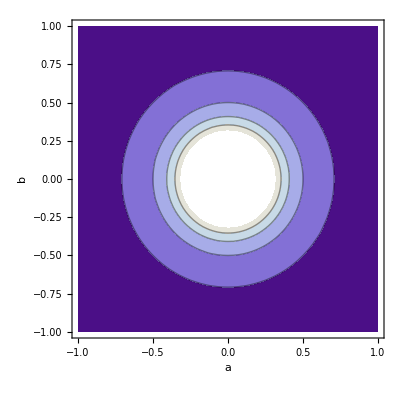

```mathematica
ContourPlot[func[a,b,1,1],{a,-1,1},{b,-1,1},AxesLabel->Automatic]
```

```mathematica
Animate[Plot[func[a,c*a,1,1],{a,0.1,0.9}],{c,0.1,0.9},AnimationRunning->False]
```

```mathematica
Simplify[func[a,c*a,1,1]]
```

1/(a^2 (1+c^2))

```mathematica
Clear[derivfuncA]
derivfuncA[a_,b_,sigmaX_,sigmaY_]=Simplify[D[func[a,b,sigmaX,sigmaY],a]]
```

-(2 a sigmaX sigmaY)/((a^2+b^2)^2)

```mathematica
Clear[derivfuncB]
derivfuncB[a_,b_,sigmaX_,sigmaY_]=Simplify[D[func[a,b,sigmaX,sigmaY],b]]
```

-(2 b sigmaX sigmaY)/((a^2+b^2)^2)

```mathematica
plot3dA=Plot3D[derivfuncA[a,b,1,1],{a,-1,1},{b,-1,1},AxesLabel->{a,b}]
```

-Graphics3D-

```mathematica
derivfuncA[a,c*a,1,1]
```

-(2 a)/((a^2+a^2 c^2)^2)